```mathematica
δ = .29;
ω =0.73;
rozw =NDSolve[{x''[t]+ 2δ  x'[t]+ω^2x[t]==0, x[0]== 100, x'[0] == 0},x, {t, 0, 20}];
```

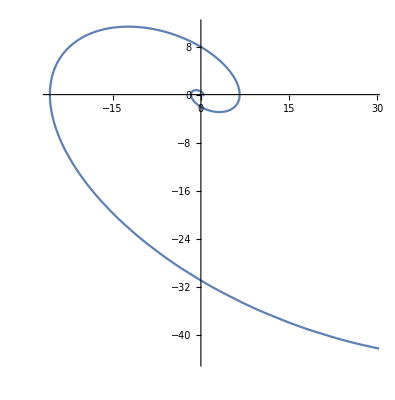

```mathematica
ParametricPlot[Evaluate[{x[t], x'[t]}/.rozw], {t, 0, 20}]
```